```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n]/Log[a]]-a n LerchPhi[a,1,1+Log[n]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a,2n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[2 n]/Log[a]]-2 a n LerchPhi[a,1,1+Log[2 n]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a,n^2]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n^2]/Log[a]]-a n^2 LerchPhi[a,1,1+Log[n^2]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[2a,n]}],{a->1}]
```

{∞}

```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a^2,n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n]/Log[a^2]]-a^(1+Log[n]/Log[a^2]) LerchPhi[a,1,1+Log[n]/Log[a^2]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a^(1/2),n]}],{a->1}]
```

{Limit[-HarmonicNumber[(2 Log[n])/Log[a]]-a n^2 LerchPhi[a,1,1+(2 Log[n])/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k^2,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n]/Log[a],2]-a n LerchPhi[a,2,1+Log[n]/Log[a]]+PolyLog[2,a],a→1]}

```mathematica
Limit[Sum[(a^k)/k^2,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-a n LerchPhi[a,2,1+Log[n]/Log[a]]+PolyLog[2,a],a→1]}

```mathematica
Limit[Sum[(a^k)/k^2,{k,Log[a,n], Infinity}],{a->1}]
```

{Limit[n HurwitzLerchPhi[a,2,Log[n]/Log[a]],a→1]}

```mathematica
{Limit[-HarmonicNumber[Log[n]/Log[a],2]+PolyLog[2,a],a->1]}
```

{Limit[-HarmonicNumber[Log[n]/Log[a],2]+PolyLog[2,a],a→1]}

```mathematica
{Limit[-HarmonicNumber[Log[100]/Log[a],2]+PolyLog[2,a],a->1]}
```

{0}

```mathematica
{Limit[-HarmonicNumber[Log[100]/Log[a],3]+PolyLog[3,a],a->1]}
```

{0}

```mathematica
{Limit[-HarmonicNumber[Log[100]/Log[a],4]+PolyLog[4,a],a->1]}
```

{0}

```mathematica
{Limit[-HarmonicNumber[Log[n]/Log[a],1]+PolyLog[1,a],a->1]}
```

```mathematica
Limit[-HarmonicNumber[Log[n]/Log[a]]-Log[1-a],a->1]
```

```mathematica
Limit[-HarmonicNumber[Log[100]/Log[a]]-Log[1-a],a->1]
```

-EulerGamma-ⅈ π-Log[Log[100]]

```mathematica
Limit[Sum[(a^k-1)/k^3,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n]/Log[a],3]-a n LerchPhi[a,3,1+Log[n]/Log[a]]+PolyLog[3,a],a→1]}

```mathematica
Limit[Sum[(a^k-1)/k^2,{k,1,Log[a,100]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[100]/Log[a],2]-100 a LerchPhi[a,2,1+Log[100]/Log[a]]+PolyLog[2,a],a→1]}

```mathematica
Limit[-HarmonicNumber[Log[100]/Log[a],2]+PolyLog[2,a],a->1]
```

0

```mathematica
Limit[Sum[(a^k-1)/k^b,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[n]/Log[a],b]-a n LerchPhi[a,b,1+Log[n]/Log[a]]+PolyLog[b,a],a→1]}

```mathematica
Limit[-HarmonicNumber[Log[n]/Log[a],b]+PolyLog[b,a],a->1]
```

Limit[-HarmonicNumber[Log[n]/Log[a],b]+PolyLog[b,a],a→1]

```mathematica
Limit[-HarmonicNumber[Log[100]/Log[a],b]+PolyLog[b,a],a->1]
```

Limit[-HarmonicNumber[Log[100]/Log[a],b]+PolyLog[b,a],a→1]

```mathematica
fb[a_,b_]:=-HarmonicNumber[Log[100]/Log[a],b]+PolyLog[b,a]
```

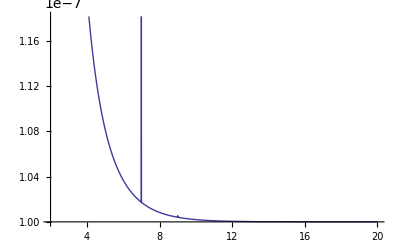

```mathematica
Plot[Re[fb[1.0000001,b]],{b,2,20}]
```

```mathematica
Limit[Sum[(a^k - 1)( k^b) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[HurwitzZeta[-b,1+Log[n]/Log[a]]-a n LerchPhi[a,-b,1+Log[n]/Log[a]]+PolyLog[-b,a]-Zeta[-b],a→1]}

```mathematica
Limit[Sum[(a^k - 1)( k^0) ,{k,1,Log[a,n]}],{a->1}]
```

{DirectedInfinity[-1+n-Log[n]]}

```mathematica
Limit[HurwitzZeta[-b,1+Log[100]/Log[a]]+PolyLog[-b,a]-Zeta[-b]/.b->1,a->1]
```

-∞

```mathematica
Limit[HurwitzZeta[-b,1+Log[n]/Log[a]]-a n LerchPhi[a,-b,1+Log[n]/Log[a]]+PolyLog[-b,a]-Zeta[-b]/.{b->-1/2,n->100},a->1]
```

$Aborted

```mathematica
Limit[Sum[(a^k )( k^b) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-a n LerchPhi[a,-b,1+Log[n]/Log[a]]+PolyLog[-b,a],a→1]}

```mathematica
Limit[Sum[(a^k )( k^b) ,{k,Log[a,n],Infinity}],{a->1}]
```

{Limit[n HurwitzLerchPhi[a,-b,Log[n]/Log[a]],a→1]}

```mathematica
Limit[Sum[(a^k)( k^-1) ,{k,Log[a,100],Infinity}],{a->1}]
```

{Limit[100 HurwitzLerchPhi[a,1,Log[100]/Log[a]],a→1]}

```mathematica
Limit[Sum[(a^k)( k^2) ,{k,Log[a,100],Infinity}],{a->1}]
```

{-∞}

```mathematica
lerch[z_, s_, a_] := 1/(2 a^s) + (Log[1/z]^(s-1)/z^a)Gamma[1-s, a Log[1/z]] + 2/(a^(s-1)) Integrate[ Sin[ s ArcTan[t]-t a Log[z]]/((1+t^2)^(s/2)(E^(2 Pi a t) - 1)), {t,0,Infinity}]
```

```mathematica
lch[z_,s_,a_]:=1/(2a^s)+Log[1/z]^(s-1)/z^a Gamma[1-s,a Log[1/z]]+2/(a^(s-1))Integrate[Sin[s ArcTan[t]-t a Log[z]]/( (1+t^2 )^(s/2)(E^(2 Pi a t)-1)),{t,0,Infinity}]
```

```mathematica
lch[1.00000001,1,1]
```

(18.3435-3.14159 ⅈ)+2 ∫_0^∞ -Sin[1.×10^-8 t-ArcTan[t]]/((-1+ⅇ^(2 π t)) √(1+t^2))ⅆt

```mathematica
N[2 ∫_0^∞ -Sin[9.999999889225291*^-9 t-ArcTan[t]]/((-1+ⅇ^(2 π t)) √(1+t^2))ⅆt]
```

0.0772157

```mathematica
lch[1.00000001,1,2]
```

(17.4003-3.14159 ⅈ)+2 ∫_0^∞ -Sin[2.×10^-8 t-ArcTan[t]]/((-1+ⅇ^(4 π t)) √(1+t^2))ⅆt

```mathematica
N[2 ∫_0^∞ -Sin[1.9999999778450582*^-8 t-ArcTan[t]]/((-1+ⅇ^(4 π t)) √(1+t^2))ⅆt]
```

0.0203628

```mathematica
lch[a,1,Log[n]/Log[a]]/.{n->100,a->1.0000001}
```

GCD::exact: Argument 2.89351×10^8 in GCD[0, 1, 2.89351×10^8, 2.89351×10^8] is not an exact number.

```mathematica
100((-0.30126140506335297-0.031415926535897934 ⅈ)+2 ∫_0^∞ Sin[ArcTan[t]-t Log[100]]/((-1+100^(6.283185617670301*^7 t)) √(1+t^2))ⅆt)
```

100 ((-0.301261-0.0314159 ⅈ)+2 ∫_0^∞ Sin[ArcTan[t]-t Log[100]]/((-1+100^(6.28319×10^7 t)) √(1+t^2))ⅆt)

```mathematica
N[100 (2 ∫_0^∞ Sin[ArcTan[t]-t Log[100]]/((-1+100^(6.283185617670301*^7 t)) √(1+t^2))ⅆt)]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.29781×10^-7}. NIntegrate obtained -7.08309×10^-17 and 1.36749×10^-19 for the integral and error estimates.

-1.41662×10^-14

```mathematica
lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.000001}
```

-1.×10^6+9.21034×10^6 ∫_0^∞ -Sin[t Log[100]]/(-1+100^(6.28319×10^6 t))ⅆt

```mathematica
N[(1/(100^2))(-1.0000000001583302*^6+9.210344977903306*^6 ∫_0^∞ -Sin[t Log[100]]/(-1+100^(6.283188449288612*^6 t))ⅆt)]
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.59562×10^-7}. NIntegrate obtained -9.04779×10^-15 and 5.03161×10^-18 for the integral and error estimates.

-100.

```mathematica
Gamma[1,-Log[100]]
```

100

```mathematica
lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.001}
```

```mathematica
-999.999916708291+9214.944775018343 ∫_0^∞ -Sin[t Log[100]]/(-1+100^(6286.326376496726 t))ⅆt
```

```mathematica
N[-999.999916708291+9214.944775018343 ∫_0^∞ -Sin[t Log[100]]/(-1+100^(6286.326376496726 t))ⅆt]
```

NIntegrate::deorela: The relative error 4.12188 is larger than expected for the integrand -Sin[t\ Log[100]]/-1 + 100^6286.33\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

-1000.

```mathematica
lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.0001}
```

-10000.+92108. ∫_0^∞ -Sin[t Log[100]]/(-1+100^(62835. t))ⅆt

```mathematica
lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.00001}
```

-100000.+921039. ∫_0^∞ -Sin[t Log[100]]/(-1+100^(628322. t))ⅆt

```mathematica
N[1/(100^2)]
```

0.0001

```mathematica
.01^2
```

0.0001

```mathematica
lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.0001}
```

-10000.+92108. ∫_0^∞ -Sin[t Log[100]]/(-1+100^(62835. t))ⅆt

```mathematica
N[-9999.999991678147+92108.00881320897 ∫_0^∞ -Sin[t Log[100]]/(-1+100^(62834.99461209911 t))ⅆt]
```

NIntegrate::deorela: The relative error 2.68551 is larger than expected for the integrand -Sin[t\ Log[100]]/-1 + 100^62835.\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
(-1/(100^1))(-10000.000000011063)
```

100.

NIntegrate::deorela: The relative error 2.68551 is larger than expected for the integrand -Sin[t\ Log[100]]/-1 + 100^62835.\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

0.01

```mathematica
(-1/(10^3))lch[a,0,Log[100]/Log[a]]/.a->(1+.1^3)
```

$Aborted

```mathematica
lch[a,-1,Log[n]/Log[a]]/.{n->100,a->1.000001}
```

GCD::exact: Argument 2.89352×10^7 in GCD[0, 1, 2.89352×10^7, 2.89352×10^7] is not an exact number.

General::stop: Further output of GCD :: exact will be suppressed during this calculation.

(-3.60517×10^12+0.000441506 ⅈ)+4.24152×10^13 ∫_0^∞ -(√(1+t^2) Sin[ArcTan[t]+t Log[100]])/(-1+100^(6.28319×10^6 t))ⅆt

```mathematica
N[Gamma[2,-Log[100]]]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
N[(-3.605171489461148*^12+0.0004415064544800765 ⅈ)+4.241522730599433*^13 ∫_0^∞ -(√(1+t^2) Sin[ArcTan[t]+t Log[100]])/(-1+100^(6.283188449288612*^6 t))ⅆt]
```

GCD::exact: Argument 2.89352×10^7 in GCD[0, 1, 2.89352×10^7, 2.89352×10^7] is not an exact number.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.29781×10^-7}. NIntegrate obtained -1.10125×10^-14 and 1.97953×10^-18 for the integral and error estimates.

-3.60517×10^12+0.000441506 ⅈ

```mathematica
(1/100^6)(-3.605171489461615*^12+0.0004415064544800765 ⅈ)
```

-3.60517+4.41506×10^-16 ⅈ

```mathematica
N[Gamma[2,-Log[100]]]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
{(-1/(100^1))N[lch[a,0,Log[n]/Log[a]]/.{n->100,a->1.0001}],Gamma[1,-Log[100]]}
```

NIntegrate::deorela: The relative error 2.68551 is larger than expected for the integrand -Sin[t\ Log[100]]/-1 + 100^62835.\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

{100.,100}

```mathematica
N[1/(100^4)]
```

1.×10^-8

```mathematica
{(-1/(10^1))N[lch[a,0,Log[n]/Log[a]]/.{n->10,a->1+(.1)^2}],Gamma[1,-Log[10]]}
```

Power::infy: Infinite expression 1/0. encountered.

{10.,10}

```mathematica
{(-1/(10^3))N[lch[a,0,Log[n]/Log[a]]/.{n->10,a->1+(.1)^4}],Gamma[1,-Log[10]]}
```

NIntegrate::deorela: The relative error 2.68551 is larger than expected for the integrand -Sin[t\ Log[10]]/-1 + 10^62835.\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

{10.,10}

```mathematica
N[1/7]
```

0.142857

```mathematica
{(-1/(7^3))N[lch[a,0,Log[n]/Log[a]]/.{n->7,a->1+(0.14285714285714285)^4}],Gamma[1,-Log[7]]}
```

NIntegrate::deorela: The relative error 4.04745 is larger than expected for the integrand -Sin[t\ Log[7]]/-1 + 7^15089.1\ t over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

Power::infy: Infinite expression 1/0. encountered.

{7.,7}

```mathematica
{(-1/(7^5))N[lch[a,0,Log[n]/Log[a]]/.{n->7,a->1+(0.14285714285714285)^6}],Gamma[1,-Log[7]]}
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000179875}. NIntegrate obtained -1.54698×10^-12 and 9.43804×10^-18 for the integral and error estimates.

{7.,7}

```mathematica
{(-1/(7^5))N[lch[a,0,Log[n]/Log[a]]/.{n->2,a->1+(0.14285714285714285)^6}],Gamma[1,-Log[13]]}
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000179875}. NIntegrate obtained -4.34293×10^-12 and 1.1836×10^-17 for the integral and error estimates.

{7.,13}

```mathematica
lch[a,-1,Log[n]/Log[a]]/.{n->10,a->1.001}
```

$Aborted

```mathematica
lch2[z_,s_,a_]:=1/(2a^s)+Log[1/z]^(s-1)/z^a Gamma[1-s,a Log[1/z]]
```

```mathematica
(1/10)^5lch2[a,-1,Log[n]/Log[a]]/.{n->10,a->1 + (1/10.)^3}
```

-13.0274+1.5968×10^-15 ⅈ

```mathematica
N[Gamma[2,-Log[17]]]
```

-31.1646+3.81657×10^-15 ⅈ

```mathematica
{(-1)^(r+1) (1/m)^((1-r)b-1)lch2[a,r,Log[n]/Log[a]]/.{n->m,a->1 + (1/m)^b},N[Gamma[1-r,-Log[m]]]}/.{b->5,m->27.,r->-2}
```

{169.313-4.14698×10^-14 ⅈ,169.313-4.14698×10^-14 ⅈ}

```mathematica
{(-1)^r (1/m)^(r b-1)lch2[a,1-r,Log[n]/Log[a]]/.{n->m,a->1 + (1/m)^b},N[Gamma[r,-Log[m]]]}/.{b->5,m->27.,r->3}
```

{169.313-4.14698×10^-14 ⅈ,169.313-4.14698×10^-14 ⅈ}

```mathematica
{(-1)^s m^(1-s b)lch2[a,1-s,Log[n]/Log[a]]/.{n->m,a->1 + (1/m)^b},N[Gamma[s,-Log[m]]]}/.{b->5,m->27.,s->2}
```

{-61.9876+7.59129×10^-15 ⅈ,-61.9876+7.59129×10^-15 ⅈ}

```mathematica
{(-1)^s n^(1-s b)lch2[a,1-s,Log[n]/Log[a]]/.{a->1 + (1/n)^b},N[Gamma[s,-Log[n]]]}/.{b->5,n->17.,s->3}
```

{74.1314-2.65007×10^-14 ⅈ,74.1314-2.65007×10^-14 ⅈ}

```mathematica
{(-1)^s n^(1-s a)lch2[1. + (1./n)^a,1-s,Log[n]/Log[1. + (1./n)^a]],N[Gamma[s,-Log[n]]]}/.{a->5,n->117.,s->3}
```

{1773.02-4.34264×10^-13 ⅈ,1773.01-4.34263×10^-13 ⅈ}

```mathematica
lch3[z_,s_,a_]:=Log[1/z]^(s-1)/z^a Gamma[1-s,a Log[1/z]]
```

```mathematica
{(-1)^s n^(1-s a)lch3[1. + (1./n)^a,1-s,Log[n]/Log[1. + (1./n)^a]],N[Gamma[s,-Log[n]]]}/.{a->5,n->100.,s->1}
```

{100.,100.}

```mathematica
Limit[Sum[(a^k - 1)( k^b) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[HurwitzZeta[-b,1+Log[n]/Log[a]]-a n LerchPhi[a,-b,1+Log[n]/Log[a]]+PolyLog[-b,a]-Zeta[-b],a→1]}

```mathematica
lch3[z_,s_,a_]:=Log[1/z]^(s-1)/z^a Gamma[1-s,a Log[1/z]]
lch4[z_,s_,a_]:=(-Log[z])^(s-1)/z^a Gamma[1-s,-a Log[z]]
```

```mathematica
Limit[Sum[(a^k)( k^s) ,{k,Log[a,n],Infinity}],{a->1}]
```

{Limit[n HurwitzLerchPhi[a,-s,Log[n]/Log[a]],a→1]}

```mathematica
Limit[(-1)^s n^(1-s a)Sum[(a^k - 1)( k^s) ,{k,1,Log[a,n]}]/. s->1,{a->1}]
```

```mathematica
pp[n_, s_, a_]:=(-1)^s n^(1-s a)lch3[1. + (1./n)^a,1-s,Log[n]/Log[1. + (1./n)^a]]
pp2[n_, s_, a_]:=(-1)^s n^(1-s a)lch4[1. + (1./n)^a,1-s,Log[n]/Log[1. + (1./n)^a]]
pp3[n_, s_, a_]:=(-1)^s n^(1-s a)lch4[1. + n^-a,1-s,Log[n]/Log[1. + n^-a]]
pp4[n_, s_, a_]:=(-1)^s n^(1-s a)lch4[1. + n^-a,1-s,Log[n]/Log[1. + n^-a]]
pp5[n_, s_, a_]:=(-1)^s n^(1-s a)lch4[1. + n^-a,1-s,Log[n]/Log[1. + n^-a]]
```

```mathematica
pp[100,3,4]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
pp2[100,3,4]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
pp3[100,3,4]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
pp5[100,3,4]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
N[Gamma[3,-Log[100]]]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
Limit[(-1)^s n^(1-s a)Sum[(a^k)( k^s) ,{k,Log[a,n],Infinity}],{a->1}]
```

```mathematica
n^(1-s a)/. {n->3,s->2,a->2}
```

1/27

```mathematica
n^(a(1/a-s))/. {n->3,s->2,a->2}
```

1/27

```mathematica
n^(1-s a)/n^-a
```

n^(1+a-a s)

```mathematica
n^-a n^(1+a-a s)/. {n->3,s->2,a->2}
```

1/27

```mathematica
FullSimplify[1+a-a s]
```

1+a-a s

```mathematica
Expand[Log[n^(1+a-a s)]/Log[n^a]]
```

```mathematica
v1[n_,a_,s_]:=Log[n^(1+a-a s)]/Log[n^-a]
```

```mathematica
N[v1[100,2,3]]
```

1.5

```mathematica
v2[n_,a_,s_]:=Log[n^(1+a-a s)]/(-a Log[n])
```

```mathematica
N[v2[100,2,3]]
```

1.5

```mathematica
v3[n_,a_,s_]:=((1+a-a s)Log[n])/(-a Log[n])
```

```mathematica
N[v3[100,2,3]]
```

1.5

```mathematica
v4[n_,a_,s_]:=(1+a-a s)/-a
```

```mathematica
N[v4[100,2,3]]
```

1.5

```mathematica
lch4[z_,s_,a_]:=(-Log[z])^(s-1)/z^a Gamma[1-s,-a Log[z]]
pp6[n_, s_, a_]:=(-1)^s n^(1-s a)lch4[1. + t,1-s,Log[n]/Log[1. + t]]/.t->n^-a
pp7[n_, s_, a_]:=(-1)^s t n^(1+a-a s)lch4[1. + t,1-s,Log[n]/Log[1. + t]]/.t->n^-a
pp8[n_, s_, a_]:=(-1)^s t^(s-a^-1)lch4[1. + t,1-s,Log[n]/Log[1. + t]]/.t->n^-a
pp9[n_, s_, a_]:=(-1)^s n a^s lch4[1.+a,1-s,Log[1+a,n]]
pp10[n_, s_, a_]:=(-1)^s n a^s lch[1.+a,1-s,Log[1+a,n]]
pp11[n_, s_, a_]:=(-1)^s n (a-1)^s lch4[a,1-s,Log[a,n]]
```

```mathematica
pp6[10,2,4]
```

-13.0272+1.59537×10^-15 ⅈ

```mathematica
pp9[164,2,.00001]
```

-672.385+8.23434×10^-14 ⅈ

```mathematica
pp10[10,1,.00001]
```

10.+0. ⅈ

```mathematica
pp10[10,2,.00001]
```

-13.0259+1.59522×10^-15 ⅈ

```mathematica
N[Gamma[2,-Log[10]]]
```

-13.0259+1.59521×10^-15 ⅈ

```mathematica
pp11[164,2,1.00001]
```

-672.385+8.23434×10^-14 ⅈ

```mathematica
pp5[100,2,4]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
pp6[100,2,4]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
pp7[100,2,4]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
pp8[100,2,4]
```

-360.517+4.41506×10^-14 ⅈ

```mathematica
n^(1-s a)/n^-a
```

```mathematica
FullSimplify[n^(1+a-a s)]
```

n^(1+a-a s)

```mathematica
Log[n^(1-s a)]/Log[n^-a]
```

```mathematica
Log[n^(1-a s)]/Log[n^-a]
```

```mathematica
E^((1-a s)/(-a))
```

ⅇ^(-(1-a s)/a)

```mathematica
n^(1-s a)/n^-a
```

n^(1+a-a s)

```mathematica
n^(1-s a)/. {n->100,s->2,a->2}
```

1/1000000

```mathematica
n^(1-s a)/. {n->100,s->2,a->2, t->n^-a}
```

1/1000000

```mathematica
n^(1-s a)/n^-a
```

n^(1+a-a s)

```mathematica
t=n^-a
```

n^-a

```mathematica
(n^(1+a-a s) t)/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^Log[n^(1+a-a s) t]/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^(Log[n^(1+a-a s)]+Log[ t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^((1+a-a s)Log[n]+Log[ t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^((1+a-a s)/-a * -a Log[n]+Log[ t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^((1+a-a s)/-a * Log[t]+Log[ t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
E^(((1+a-a s)/-a+1)Log[ t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
Expand[((1+a-a s)/-a+1)]
```

-1/a+s

```mathematica
E^((-1/a+s)Log[t])/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
t^((-1/a+s))/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
t^(s-a^-1)/. { n->100,s->2,a->2}
```

1/1000000

```mathematica
FullSimplify[(n^-a)^(s-a^-1)]
```

(n^-a)^(-1/a+s)

```mathematica
3^7
```

2187

```mathematica
-Log[3,2187]^-1
```

-1/7

```mathematica
FullSimplify[(-1)^s n^2 t^(s-Log[n,t]^-1)]
```

(-1)^s n t^s

```mathematica
lch[z_,s_,a_]:=1/(2a^s)+Log[1/z]^(s-1)/z^a Gamma[1-s,a Log[1/z]]+2/(a^(s-1))Integrate[Sin[s ArcTan[t]-t a Log[z]]/( (1+t^2 )^(s/2)(E^(2 Pi a t)-1)),{t,0,Infinity}]
```

```mathematica
Limit[Sum[(a^k)( k^(s-1)) ,{k,Log[a,n],Infinity}],{a->1}]
```

{Limit[n HurwitzLerchPhi[a,1-s,Log[n]/Log[a]],a→1]}

```mathematica
Limit[(-1)^s  Sum[(a-1)^s(a^k)( k^(s-1)) ,{k,Log[a,n],Infinity}],{a->1}]
```

{Limit[(-1)^s (-1+a)^s n HurwitzLerchPhi[a,1-s,Log[n]/Log[a]],a→1]}

```mathematica
so[n_,s_,a_]:=(-1)^s (-1+a)^s n HurwitzLerchPhi[a,1-s,Log[n]/Log[a]]
```

```mathematica
so[100,2,1.00001]
```

-360.518+1.22466×10^-16 ⅈ

```mathematica
N[Gamma[3,-Log[100]]]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
so2[n_, s_, a_] := (-1)^s (a-1)^s  Sum[ (a^k -1)( k^(s-1)) ,{k,1,Log[a,n]}]
```

```mathematica
so2[100,0,1.000001]
```

28.0218-2.46016×10^-10 ⅈ

```mathematica
so2[100, 1,1.000001]
```

-94.3949

```mathematica
so3[n_, s_, a_] := (-1)^s  Sum[ (a-1)^s (a^k -1)( k^(s-1)) ,{k,1,Log[a,n]}]
so3a[n_, s_, a_] := (-1)^s  (a-1)^s  Sum[ (a^k -1)( k^(s-1)) ,{k,1,Log[a,n]}]
```

```mathematica
so3[100,0,1.000001]
```

28.0218-2.46016×10^-10 ⅈ

```mathematica
so3a[100,0,1.000001]
```

28.0218-2.46016×10^-10 ⅈ

```mathematica
so3[100,1,1.000001]-(1+Log[100])
```

-100.

```mathematica
so3a[100,1,1.000001]-(1+Log[100])
```

-100.

```mathematica
so3[100,2,1.00001]-(1-Log[n]^2/2/.n->100)
```

360.521

```mathematica
Limit[(-1)^s  Sum[(a-1)^s(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]+a n LerchPhi[a,1-s,1+Log[n]/Log[a]]-PolyLog[1-s,a]),a→1]}

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a]),a->1]
```

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->0,a->1]
```

Limit[-HarmonicNumber[Log[n]/Log[a]]-Log[1-a],a→1]

```mathematica
Limit[-HarmonicNumber[Log[100]/Log[a]]-Log[1-a],a->1]
```

-EulerGamma-ⅈ π-Log[Log[100]]

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->1,a->1]
```

1+Log[n]

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->2,a->1]
```

1-Log[n]^2/2

```mathematica
Expand[Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->3,a->1]]
```

2+Log[n]^3/3

```mathematica
N[1+Log[n]/.n->100]
```

5.60517

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->4,a->1]
```

6-Log[n]^4/4

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->5,a->1]
```

24+Log[n]^5/5

```mathematica
Limit[-(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]-PolyLog[1-s,a])/.s->6,a->1]
```

120-Log[n]^6/6

```mathematica
so4[n_, s_, a_] := (-1)^(s+1)  Sum[(a-1)^s(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] + Gamma[s]-(-1)^(s) Log[n]^s/s
```

```mathematica
so4a[n_, s_, a_] := (-1)^(s+1) (a-1)^s Sum[(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] + Gamma[s]-(-1)^(s) Log[n]^s/s
```

```mathematica
so4a[100,4,1.00001]
```

-5567.41

```mathematica
N[Gamma[4,-Log[100]]]
```

-5567.28+2.04539×10^-12 ⅈ

```mathematica
FullSimplify[(-1)^(s+1)  Sum[(a-1)^s(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] + Gamma[s]+(-1)^(s+1) Log[n]^s/s]
```

Gamma[s]-((-1)^s Log[n]^s)/s+(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]+a n LerchPhi[a,1-s,1+Log[n]/Log[a]]-PolyLog[1-s,a])

```mathematica
so5[n_, s_, a_]:=Gamma[s]-((-1)^s Log[n]^s)/s+(-1)^s (-1+a)^s (HarmonicNumber[Log[n]/Log[a],1-s]+a n LerchPhi[a,1-s,1+Log[n]/Log[a]]-PolyLog[1-s,a])
```

```mathematica
so5[200,3,1.00001]
```

3895.19+4.89866×10^-16 ⅈ

```mathematica
N[Gamma[3,-Log[200]]]
```

3895.11-9.54026×10^-13 ⅈ

```mathematica
(-1)^(s+1) (a-1)^s Sum[(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] + Gamma[s]-(-1)^(s) Log[n]^s/s
```

Gamma[s]-((-1)^s Log[n]^s)/s+(-1)^(1+s) (-1+a)^s (-HarmonicNumber[Log[n]/Log[a],1-s]-a n LerchPhi[a,1-s,1+Log[n]/Log[a]]+PolyLog[1-s,a])

```mathematica
FullSimplify[(-1)^(s+1) (a-1)^s Fn + Gamma[s]-(-1)^(s) Log[n]^s/s]
```

Gamma[s]-((-1)^s ((-1+a)^s Fn s+Log[n]^s))/s

```mathematica
FullSimplify[Gamma[s] s]
```

Gamma[1+s]

```mathematica
so6[n_, s_, a_]:=(s!-(-1)^s ((-1+a)^s Sum[(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] s+Log[n]^s))/s
```

```mathematica
so6[100,3,1.00001]
```

1399.75

```mathematica
N[Gamma[3,-Log[100]]]
```

1399.73-3.42834×10^-13 ⅈ

```mathematica
so7[n_, s_, a_] :=(-1)^(s+1)  Sum[(a-1)^s(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] + Gamma[s]+(-1)^(s+1) Log[n]^s/s
```

```mathematica
so7[100,2,1.0001]
```

```mathematica
so8[n_, s_, a_] :=(-1)^s  Sum[(a-1)^s(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] +(-1)^(s) Log[n]^s/s
```

```mathematica
so8[130,4,1.0001]
```

8776.14

```mathematica
N[Gamma[4,0,-Log[130]]]
```

8774.82-3.22161×10^-12 ⅈ

```mathematica
so9[n_, s_, a_] :=(-1)^s ( (a-1)^s Sum[(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] +Log[n]^s/s)
```

```mathematica
so9[130,4,1.0001]
```

8776.14

```mathematica
Limit[(-1)^b  Sum[(a^(1-b)-1)^b((a)^k-1)( k^(b-1)) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-(-1)^b (-1+a^(1-b))^b (HarmonicNumber[Log[n]/Log[a],1-b]+a n LerchPhi[a,1-b,1+Log[n]/Log[a]]-PolyLog[1-b,a]),a→1]}

```mathematica
Limit[(-1)^s  Sum[(a^(1-t)-1)^s((a^(1-t))^k-1)( k^(s-1)) ,{k,1,Log[a,n]}],{a->1}]
```

{Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]+a (a^(1-t))^(Log[n]/Log[a]) LerchPhi[a^(1-t),1-s,1+Log[n]/Log[a]]-a^t PolyLog[1-s,a^(1-t)]),a→1]}

```mathematica
Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)]),a->1]
```

Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)]),a→1]

```mathematica
Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->0,a->1]
```

Limit[-a^-t (a^t HarmonicNumber[Log[n]/Log[a]]+a^t Log[1-a^(1-t)]),a→1]

```mathematica
Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->1,a->1]
```

1+Log[n]-t Log[n]

```mathematica
Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->2,a->1]
```

```mathematica
FullSimplify[1-1/2 (-1+t)^2 Log[n]^2]
```

1-1/2 (-1+t)^2 Log[n]^2

```mathematica
Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->3,a->1]
```

```mathematica
FullSimplify[1/3 (6-(-1+t)^3 Log[n]^3)]
```

2-1/3 (-1+t)^3 Log[n]^3

```mathematica
FullSimplify[Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->4,a->1]]
```

6-1/4 (-1+t)^4 Log[n]^4

```mathematica
FullSimplify[Limit[-(-1)^s a^-t (-1+a^(1-t))^s (a^t HarmonicNumber[Log[n]/Log[a],1-s]-a^t PolyLog[1-s,a^(1-t)])/.s->5,a->1]]
```

24-1/5 (-1+t)^5 Log[n]^5

```mathematica
N[Gamma[2.5,0,-Log[130]]]
so9[n_, s_, a_] :=(-1)^s ( (a-1)^s Sum[(a^k-1)( k^(s-1)) ,{k,1,Log[a,n]}] +Log[n]^s/s)
so9[130,2.5,1.0001]
```

3.11437×10^-13+1017.23 ⅈ

3.11464×10^-13+1017.32 ⅈ

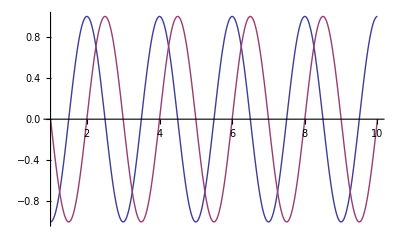

```mathematica
Plot[{Re[(-1)^(j ) ],Im[(-1)^(j) ]},{j,1,10}]
```

```mathematica
Plot[{Cos[j Pi], Sin[j Pi]},{j,1,10}]
```

-Graphics-